```mathematica
%%%Ref. 1: T. Schoenenbach, et al, MNRAS 430 (2013), 2999-3009%%%
```

```mathematica
%%%Ref 2: T. Schoenenbach et al., MNRAS 442 (2014), 121-130
```

```mathematica
%%%Later, calculation is restricted to the orbital plane \theta=pi/2
%%% Massunit m=1-> r is in units of m
```

```mathematica
%%%For the definition of Sigma, Psi, Delta and the metric see Ref. 1%%%
```

```mathematica
Sigma[r_,a_,theta_]:=r^2 +a^2 Cos[theta]^2
Psi[r_,B_,m_]:= 2*m*r - B/(2*r)
Delta[r_,a_,B_,m_]:= r^2 +a^2 - Psi[r,B,m]
```

```mathematica
g00[r_,a_,B_,m_,theta_]:=-(1 - Psi[r,B,m]/Sigma[r,a,theta])
g11[r_,a_,B_,m_,theta_]:=Sigma[r,a,theta]/Delta[r,a,B,m]
g22[r_,a_,theta_]:=Sigma[r,a,theta]
g33[r_,a_,B_,m_,theta_]:=(r^2+a^2+ (a^2Psi[r,B,m])/Sigma[r,a,theta]*Sin[theta]^2)Sin[theta]^2
g03[r_,a_,B_,m_,theta_]:=-a Psi[r,B,m]/Sigma[r,a,theta]*Sin[theta]^2
```

```mathematica
%%%definition of then function h(r), see Ref. 1, also for omegapro (pro=prograde)
%%% Domegapro=derivative of omegaprp with respect to r
```

```mathematica
hauxiliary[r_,B_,m_]:=2*m/r^2  -(3 B)/(2r^4)
omegapro[r_,a_,B_,m_]:=1/(a+ Sqrt[2*r/(hauxiliary[r,B,m])])
omegaretro[r_,a_,B_,m_]:=1/(a- Sqrt[2*r/(hauxiliary[r,B,m])])
```

```mathematica
Domegapro[r_,a_,B_,m_]:=D[1/(a+ Sqrt[2*x/(hauxiliary[x,B,m])]),x]/.x->r
```

```mathematica
%%%Formulas for the Energy, Angular momneta: See Ref. 2, Section 2.1
```

```mathematica
denominatorpro[r_,a_,B_,m_,theta_]:=-g33[r,a,B,m,theta]omegapro[r,a,B,m]^2 -2*g03[r,a,B,m,theta]*omegapro[r,a,B,m] - g00[r,a,B,m,theta]
denominatorretro[r_,a_,B_,m_,theta_]:=-g33[r,a,B,m,theta]omegaretro[r,a,B,m]^2 -2*g03[r,a,B,m,theta]*omegaretro[r,a,B,m] - g00[r,a,B,m,theta]
Esquaredpro[r_,a_,B_,m_,theta_]:=(g00[r,a,B,m,theta]+omegapro[r,a,B,m]*g03[r,a,B,m,theta])^2/denominatorpro[r,a,B,m,theta]
Esquaredretro[r_,a_,B_,m_,theta_]:=(g00[r,a,B,m,theta]+omegaretro[r,a,B,m]*g03[r,a,B,m,theta])^2/denominatorretro[r,a,B,m,theta]
Lsquaredpro[r_,a_,B_,m_,theta_]:=(g03[r,a,B,m,theta]+omegapro[r,a,B,m]*g33[r,a,B,m,theta])^2/denominatorpro[r,a,B,m,theta]
Lsquaredretro[r_,a_,B_,m_,theta_]:=(g03[r,a,B,m,theta]+omegaretro[r,a,B,m]*g33[r,a,B,m,theta])^2/denominatorretro[r,a,B,m,theta]
```

```mathematica
Epro[r_,a_,B_]:=-(g00[r,a,B,1,Pi/2]+omegapro[r,a,B,1]*g03[r,a,B,1,Pi/2])/Sqrt[denominatorpro[r,a,B,1,Pi/2]]
Lpro[r_,a_,B_]:=(g03[r,a,B,1,Pi/2]+omegapro[r,a,B,1]*g33[r,a,B,1,Pi/2])/Sqrt[denominatorpro[r,a,B,1,Pi/2]]
Lretro[r_,a_,B_]:=(g03[r,a,B,1,Pi/2]+omegaretro[r,a,B,1]*g33[r,a,B,1,Pi/2])/Sqrt[denominatorretro[r,a,B,1,Pi/2]]
```

```mathematica
DourEpro[r_,a_,B_,m_]:=D[Sqrt[Esquaredpro[x,a,B,m ,Pi/2]],x]/.x->r
DourLpro[r_,a_,B_,m_]:=D[Sqrt[Lsquaredpro[x,a,B,m ,Pi/2]],x]/.x->r
DourLpro2[r_,a_,B_,m_]:=D[Lpro[x,a,B],x]/.x->r
```

```mathematica
%%%Define intensity as in eq. (22) of Ref. 2
```

```mathematica
EminusOL[r_,a_,B_]:= Epro[r,a,B]-omegapro[r,a,B,1]*Lpro[r,a,B]
integrandf[r_,a_,B_]:=EminusOL[r,a,B]*DourLpro2[r,a,B,1]
f[r_,a_,B_,rms_]:=-(Domegapro[r,a,B,1]/EminusOL[r,a,B]^2)*NIntegrate[integrandf[x,a,B],{x,rms,r},WorkingPrecision->5]
```

```mathematica
Domegapro[r,a,B,1]
```

-(1/(-(3 B)/(2 r^4)+2/r^2)-(((6 B)/r^5-4/r^3) r)/((-(3 B)/(2 r^4)+2/r^2)^2))/(√2 √(r/(-(3 B)/(2 r^4)+2/r^2)) (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)

```mathematica
zzz=Simplify[%]
```

(3 r^4 (5 B-4 r^2))/((3 B-4 r^2)^2 √(r^5/(-3 B+4 r^2)) (a+2 √(r^5/(-3 B+4 r^2)))^2)

```mathematica
EminusOL[r,a,B]
```

(1-(-B/(2 r)+2 r)/r^2+(a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))))/(√(1-(-B/(2 r)+2 r)/r^2+(2 a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)))-(-(a (-B/(2 r)+2 r))/r^2+(a^2+r^2+(a^2 (-B/(2 r)+2 r))/r^2)/(a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))) √(1-(-B/(2 r)+2 r)/r^2+(2 a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)))

```mathematica
yyy=1/Simplify[%]^2
```

((3 B-4 r^2) (a+2 √(r^5/(-3 B+4 r^2)))^2)/(B (-5 r^2+12 a √(r^5/(-3 B+4 r^2)))-4 (-3 r^4+r^5+4 a r^2 √(r^5/(-3 B+4 r^2))))

```mathematica
yyy*zzz
```

(3 r^4 (5 B-4 r^2))/((3 B-4 r^2) √(r^5/(-3 B+4 r^2)) (B (-5 r^2+12 a √(r^5/(-3 B+4 r^2)))-4 (-3 r^4+r^5+4 a r^2 √(r^5/(-3 B+4 r^2)))))

```mathematica
%%%Final fore-factor
```

```mathematica
FullSimplify[%]
```

-(3 (-5 B+4 r^2) √(r^5/(-3 B+4 r^2)))/(B r (5 r^2-12 a √(r^5/(-3 B+4 r^2)))+4 (-3 r^5+r^6+4 a r^3 √(r^5/(-3 B+4 r^2))))

```mathematica
%%%Integrante
%%%Metodo
```

```mathematica
integrandf[r,a,B]
```

((-(a (2+B/(2 r^2)))/r^2+(2 a (-B/(2 r)+2 r))/r^3+((a^2 (2+B/(2 r^2)))/r^2+2 r-(2 a^2 (-B/(2 r)+2 r))/r^3)/(a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))-((1/(-(3 B)/(2 r^4)+2/r^2)-(((6 B)/r^5-4/r^3) r)/((-(3 B)/(2 r^4)+2/r^2)^2)) (a^2+r^2+(a^2 (-B/(2 r)+2 r))/r^2))/(√2 √(r/(-(3 B)/(2 r^4)+2/r^2)) (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2))/(√(1-(-B/(2 r)+2 r)/r^2+(2 a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)))-((-(2+B/(2 r^2))/r^2+(2 (-B/(2 r)+2 r))/r^3-(√2 a (-B/(2 r)+2 r) (1/(-(3 B)/(2 r^4)+2/r^2)-(((6 B)/r^5-4/r^3) r)/((-(3 B)/(2 r^4)+2/r^2)^2)))/(r^2 √(r/(-(3 B)/(2 r^4)+2/r^2)) (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)+(2 a (2+B/(2 r^2)))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))-(4 a (-B/(2 r)+2 r))/(r^3 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-(a^2 (2+B/(2 r^2)))/r^2-2 r+(2 a^2 (-B/(2 r)+2 r))/r^3)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)-(√2 (1/(-(3 B)/(2 r^4)+2/r^2)-(((6 B)/r^5-4/r^3) r)/((-(3 B)/(2 r^4)+2/r^2)^2)) (-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2))/(√(r/(-(3 B)/(2 r^4)+2/r^2)) (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^3)) (-(a (-B/(2 r)+2 r))/r^2+(a^2+r^2+(a^2 (-B/(2 r)+2 r))/r^2)/(a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))))/(2 (1-(-B/(2 r)+2 r)/r^2+(2 a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2))^(3/2))) ((1-(-B/(2 r)+2 r)/r^2+(a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))))/(√(1-(-B/(2 r)+2 r)/r^2+(2 a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2)))-(-(a (-B/(2 r)+2 r))/r^2+(a^2+r^2+(a^2 (-B/(2 r)+2 r))/r^2)/(a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))) √(1-(-B/(2 r)+2 r)/r^2+(2 a (-B/(2 r)+2 r))/(r^2 (a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2))))+(-a^2-r^2-(a^2 (-B/(2 r)+2 r))/r^2)/((a+√2 √(r/(-(3 B)/(2 r^4)+2/r^2)))^2))))

```mathematica
yyy=FullSimplify[%]
```

-((12 a r^3 (5 B-4 r^2) (B+2 (-2+r) r^2)+24 a^3 (5 B r^4-4 r^6)+√(r^5/(-3 B+4 r^2)) (5 B+4 (-3+r) r^2) (15 B^2-8 (-6+r) r^4-2 B r^2 (20+3 r))+2 a^2 r √(r^5/(-3 B+4 r^2)) (69 B^2+16 r^4 (7+3 r)-12 B r^2 (12+5 r)))/(2 r^4 (25 B^2+8 B r (6 a^2+5 (-3+r) r)+16 r^3 (-4 a^2+(-3+r)^2 r))))

```mathematica
%%%Plot of intensities, here a=0.9 (maybe changed), b=64/27, integration of r starts for pc-GR at 4/3=1.334 (position where omega=0)and end at r=15. For GR (a=0, second part) integrations starts at the value of the last stable orbit (changes with a!) and ends also at r=15
```

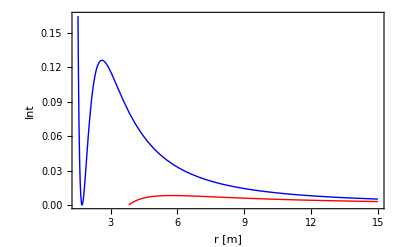

```mathematica
Show[{Plot[f[r,0.9,64/27,1.72],{r,1.334,15},AxesOrigin->{0,0},PlotStyle->{{Thickness[Large],Blue}}],Plot[f[r,0.9,0,3.81529],{r,3.81529,15},AxesOrigin->{0,0},PlotStyle->{{Thickness[Large],Red}}]},Frame-> True,FrameLabel->{"r [m]", "Int"}, PlotRange-> All,FrameTicksStyle-> Directive[Blue,18]]
```

```mathematica
%%%Separated plots for pc-GR and then GR.
```

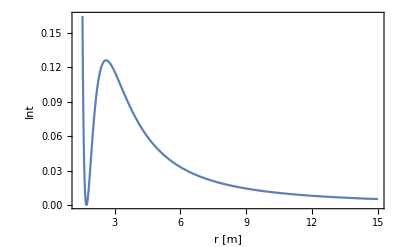

```mathematica
Plot[f[r,0.9,64/27,1.72],{r,1.334,15},Frame-> True,FrameLabel->{"r [m]", "Int"}, FrameTicksStyle-> Directive[Blue,18]]
```

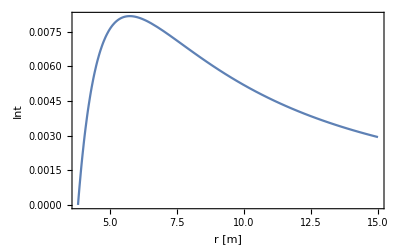

```mathematica
Plot[f[r,0.9,0,3.81529],{r,3.81529,15},Frame-> True,FrameLabel->{"r [m]", "Int"}, FrameTicksStyle-> Directive[Blue,18]]
```